Run the code to draw 100 random circles in a size 10 region. Try a different number of circles:

l

This draws a circle at coordinate {5,5}. PlotRangepaclet:ref/PlotRange specifies the size of the drawing area:

Graphics[Circle[{5,5}],PlotRange→{{0,10},{0,10}}]

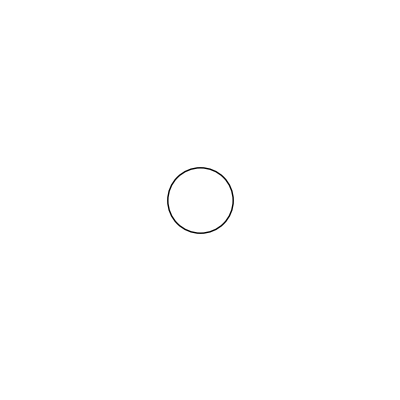

Use RandomRealpaclet:ref/RandomReal to draw circles at random positions.

This gives a random number between 0 and 10. Each time you run the code, you get a different number:

RandomReal[10]

0.166201

This gives a list of two random numbers:

RandomReal[10,2]

{5.55267,2.74885}

This draws a circle at a random position. Each time you run the code, the circle is drawn in a different place:

Graphics[Circle[RandomReal[10,2]],PlotRange→{{0,10},{0,10}}]

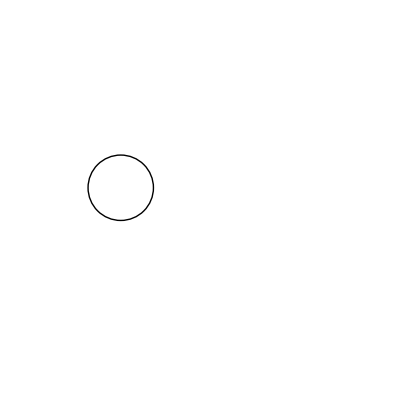

Use Tablepaclet:ref/Table to draw lots of circles. Tablepaclet:ref/Table makes lists of things.

This gives a list of 10 random coordinate positions:

Table[RandomReal[10,2],{10}]

{{7.37798,1.14643},{7.50482,0.472984},{4.02266,4.87548},{8.72133,4.21485},{8.34656,0.712854},{4.89501,1.12845},{5.955,0.0414142},{4.09103,4.96259},{4.24861,1.23551},{2.09164,0.161947}}

This draws 10 circles in random coordinate positions:

Graphics[Table[Circle[RandomReal[10,2]],{10}],PlotRange→{{0,10},{0,10}}]

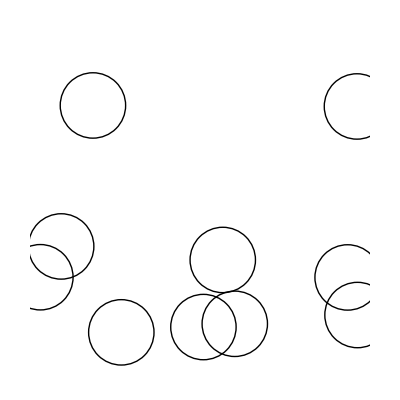

If you don’t specify a PlotRangepaclet:ref/PlotRange, the output will be just large enough to contain all the circles:

Graphics[Table[Circle[RandomReal[10,2]],{10}]]

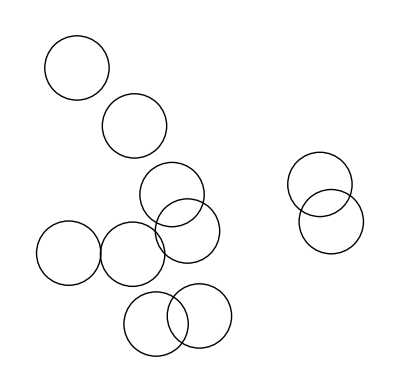

l

## -Graphics- -Graphics- -Graphics-

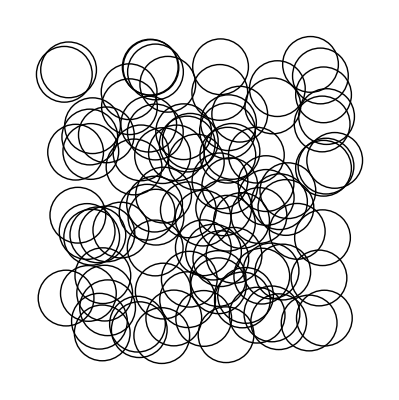

```mathematica
Graphics[Table[Circle[RandomReal[10,2]],{100}]]
```

```mathematica
Rasterize[%29,"Image"]
```

-Graphics-

Use circles with random radii up to 1.5. Try ranges of radii other than 1.5:

l

This draws a circle at {5,5} with a radius of 1.5:

Graphics[Circle[{5,5},1.5],PlotRange→{{0,10},{0,10}}]

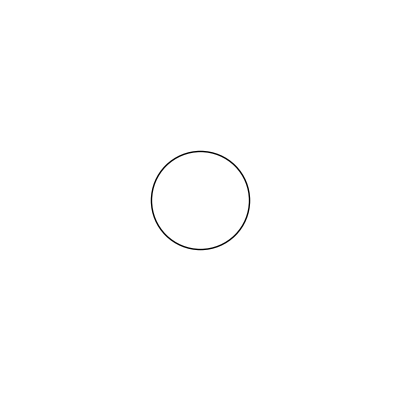

Use RandomRealpaclet:ref/RandomReal to specify a random radius. Each time you run the code, you get a different size of circle with a radius between 0 and 1.5:

Graphics[Circle[{5,5},RandomReal[1.5]],PlotRange→{{0,10},{0,10}}]

-Graphics-

Make both the positions and the radii of the circles random:

Graphics[Table[Circle[RandomReal[10,2],RandomReal[1.5]],{100}]]

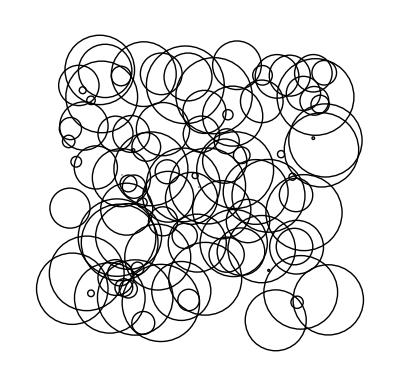

l

## -Graphics- -Graphics- -Graphics-

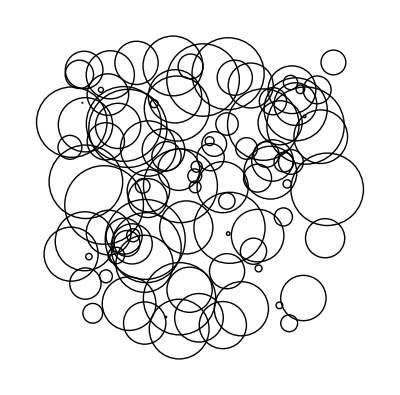

```mathematica
Graphics[Table[Circle[RandomReal[10,2],RandomReal[1.5]],{100}]]
```

Use random colors, and use disks instead of circles. Try numbers of disks other than 100:

l

Use Diskpaclet:ref/Disk instead of Circlepaclet:ref/Circle to get a filled-in shape:

Graphics[Disk[{5,5}]]



Make the disk red:

Graphics[{Red,Disk[{5,5}]}]



Make the disk a random color. Each time you run the code, you get a different color of disk:

Graphics[{RandomColor[],Disk[{5,5}]}]

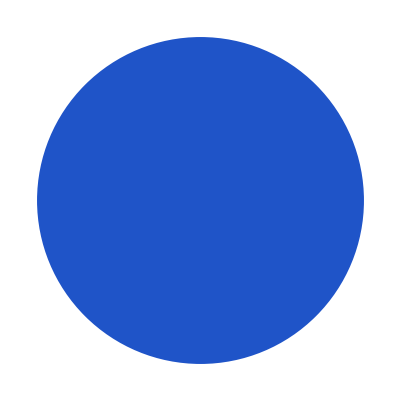

Make disks with random colors, random positions, and random sizes:

Graphics[Table[{RandomColor[],Disk[RandomReal[10,2],RandomReal[1.5]]},{100}]]

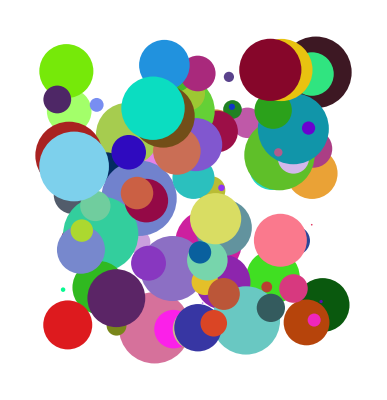

l

## -Graphics- -Graphics- -Graphics-

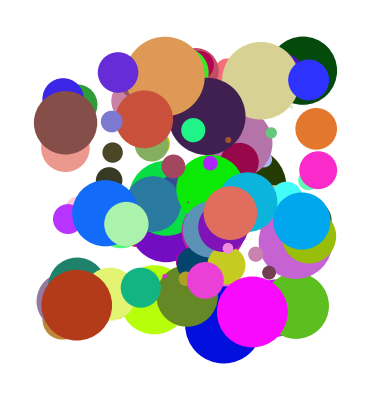

```mathematica
Graphics[Table[{RandomColor[],Disk[RandomReal[10,2],RandomReal[1.5]]},{100}]]
```

Make each disk have 50% opacity. Try different opacities:

l

Add Opacity[.5] to make the disks 50% opaque (which is 50% transparent):

Graphics[Table[{RandomColor[],Opacity[.5],Disk[RandomReal[10,2],RandomReal[1.5]]},{100}]]

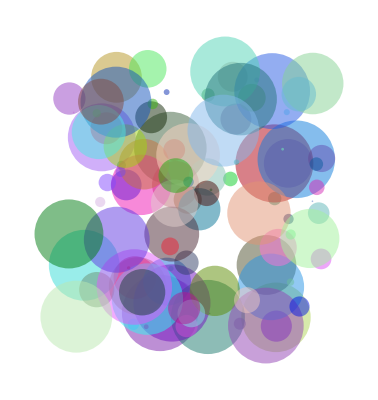

l

## -Graphics- -Graphics- -Graphics-

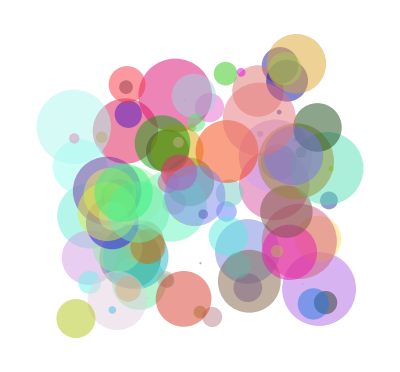

```mathematica
Graphics[Table[{RandomColor[],Opacity[.5],Disk[RandomReal[10,2],RandomReal[1.5]]},{100}]]
```

Share It — Make a website that gives a different “circlescape” each time it’s visited:

l

Deploy the “circlescape” code to the Wolfram Cloud where anyone with a browser can use it:

CloudDeploy[
Delayed[ExportForm[
Graphics[Table[{RandomColor[],Opacity[.5],Disk[RandomReal[10,2],RandomReal[1.5]]},{100}]],
"PNG"]],
"Permissions"→"Public"
]

CloudObject[]

Click the link in the output to visit the site. Refresh the page in your browser to get a new circlescape.

Tell the world about your creation by sharing the link via email, tweet, or other message.

l

## -Graphics- -Graphics- -Graphics-

```mathematica
CloudDeploy[
Delayed[ExportForm[
Graphics[Table[{RandomColor[],Opacity[.5],Disk[RandomReal[10,2],RandomReal[1.5]]},{100}]],
"PNG"]],
"Permissions"->"Public"
]
```

CloudObject[]

Explore this further or try another exploration!